```mathematica
Manipulate[Plot[{r*Cosh[x],x/2},{x,-4,4},PlotRange->{{-4,4},{-3,3}}],{r,-1,1}]
```

```mathematica
ss1=Table[{r,x/.FindRoot[r*Cosh[x]-x/2==0,{x,0}]},{r,0.1,0.33137,0.0001}];
```

```mathematica
ss2=Table[{r,x/.FindRoot[r*Cosh[x]-x/2==0,{x,10}]},{r,0.1,0.33137,0.0001}];
```

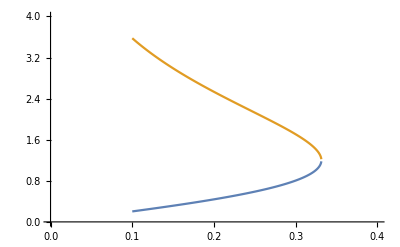

```mathematica
ListPlot[{ss1,ss2},Joined->True,PlotRange->{{0,0.4},{0,4}}]
```